# Solve

| Solvepaclet:ref/Solve[expr,vars]
attempts to solve the system expr of equations or inequalities for the variables vars. 
 | Solvepaclet:ref/Solve[expr,vars,dom]
solves over the domain dom. Common choices of dom are Realspaclet:ref/Reals, Integerspaclet:ref/Integers, and Complexespaclet:ref/Complexes.

Details and Options

The system expr can be any logical combination of:

| lhs==rhs | equations 
       | lhs!=rhs | inequations 
       | lhs>rhs or lhs>=rhs  | inequalities 
       | expr∈dom | domain specifications 
       | ForAll[x,cond,expr] | universal quantifiers 
       | Exists[x,cond,expr] | existential quantifiers

Solvepaclet:ref/Solve[{expr_1,expr_2,…},vars] is equivalent to Solvepaclet:ref/Solve[expr_1&&expr_2&&…,vars].

A single variable or a list of variables can be specified.

Solvepaclet:ref/Solve gives solutions in terms of rules of the form x→sol.

When there are several variables, the solution is given in terms of lists of rules: {x->s_x,y->s_y,…}.

When there are several solutions, Solvepaclet:ref/Solve gives a list of them.

When a single variable is specified and a particular root of an equation has multiplicity greater than one, Solvepaclet:ref/Solve gives several copies of the corresponding solution.

Solvepaclet:ref/Solve[expr,vars] assumes by default that quantities appearing algebraically in inequalities are real, while all other quantities are complex.

Solvepaclet:ref/Solve[expr,vars,dom] restricts all variables and parameters to belong to the domain dom.

If dom is Realspaclet:ref/Reals, or a subset such as Integerspaclet:ref/Integers or Rationalspaclet:ref/Rationals, then all constants and function values are also restricted to be real.

Solvepaclet:ref/Solve[expr&&vars∈Realspaclet:ref/Reals,vars,Complexespaclet:ref/Complexes] solves for real values of variables, but function values are allowed to be complex.

Solvepaclet:ref/Solve[expr,vars,Integerspaclet:ref/Integers] solves Diophantine equations over the integers.

Algebraic variables in expr free of the x_i and of each other are treated as independent parameters.

Solvepaclet:ref/Solve deals primarily with linear and polynomial equations.

When expr involves only polynomial equations and inequalities over real or complex domains, then Solvepaclet:ref/Solve can always in principle solve directly for all the x_i.

When expr involves transcendental conditions or integer domains, Solvepaclet:ref/Solve will often introduce additional parameters in its results.

Solvepaclet:ref/Solve can give explicit representations for solutions to all linear equations and inequalities over the integers, and can solve a large fraction of Diophantine equations described in the literature.

When expr involves only polynomial conditions over real or complex domains, Solvepaclet:ref/Solve[expr,vars] will always be able to eliminate quantifiers.

The following options can be given:

| Cubics | False | whether to use explicit radicals to solve all cubics
       | GeneratedParameters | C | how to name parameters that are generated 
       | InverseFunctions | Automatic | whether to use symbolic inverse functions
       | MaxExtraConditions | 0 | how many extra equational conditions on continuous parameters to allow
       | Method | Automatic | what method should be used
       | Modulus | 0 | modulus to assume for integers
       | Quartics | False | whether to use explicit radicals to solve all quartics
       | VerifySolutions | Automatic | whether to verify solutions obtained using non-equivalent transformations
       | WorkingPrecision | Infinity | precision to be used in computations

Solvepaclet:ref/Solve gives generic solutions only. Solutions that are valid only when continuous parameters satisfy equations are removed. Other solutions that are only conditionally valid are expressed as ConditionalExpressionpaclet:ref/ConditionalExpression objects.

Conditions included in ConditionalExpressionpaclet:ref/ConditionalExpression solutions may involve inequalities, Elementpaclet:ref/Element statements, equations and inequations on non-continuous parameters, and equations with full-dimensional solutions. Inequations and NotElementpaclet:ref/NotElement conditions on continuous parameters and variables are dropped.

With MaxExtraConditionspaclet:ref/MaxExtraConditions->Automaticpaclet:ref/Automatic, only solutions that require the minimal number of equational conditions on continuous parameters are included.

With MaxExtraConditionspaclet:ref/MaxExtraConditions->Allpaclet:ref/All, solutions that require arbitrary conditions on parameters are given and all conditions are included.

With MaxExtraConditionspaclet:ref/MaxExtraConditions->k, only solutions that require at most k equational conditions on continuous parameters are included.

Solvepaclet:ref/Solve uses non-equivalent transformations to find solutions of transcendental equations and hence it may not find some solutions and may not establish exact conditions on the validity of the solutions found.

With Methodpaclet:ref/Method->Reducepaclet:ref/Reduce, Solvepaclet:ref/Solve uses only equivalent transformations and finds all solutions.

Solvepaclet:ref/Solve gives {} if there are no possible solutions to the equations.

Solvepaclet:ref/Solve gives {{}} if the set of solutions is full-dimensional.

Solvepaclet:ref/Solve[eqns,…,Modulus->m] solves equations over the integers modulo m. With Moduluspaclet:ref/Modulus->Automaticpaclet:ref/Automatic, Solvepaclet:ref/Solve will attempt to find the largest modulus for which the equations have solutions.

Solvepaclet:ref/Solve uses special efficient techniques for handling sparse systems of linear equations with approximate numerical coefficients.

## Examples (105)

### Basic Examples (6)

Solve a quadratic equation:

```mathematica
Solve[x^2+a x+1==0,x]
```

{{x→1/2 (-a-√(-4+a^2))},{x→1/2 (-a+√(-4+a^2))}}

Solve simultaneous equations in x and y:

```mathematica
Solve[a x+y==7&&b x-y==1,{x,y}]
```

{{x→8/(a+b),y→-(a-7 b)/(a+b)}}

Solutions are given as lists of replacements:

```mathematica
sol=Solve[x^2+y^2==1&&x+y==a,{x,y}]
```

{{x→1/2 (a-√(2-a^2)),y→1/2 (a+√(2-a^2))},{x→1/2 (a+√(2-a^2)),y→1/2 (a-√(2-a^2))}}

Replace x by solutions:

```mathematica
x/.sol
```

{1/2 (a-√(2-a^2)),1/2 (a+√(2-a^2))}

Replace combinations of x and y by solutions, and simplify the results:

```mathematica
{x-y,x^2-y^2}/.sol//FullSimplify
```

{{-√(2-a^2),-a √(2-a^2)},{√(2-a^2),a √(2-a^2)}}

Plot the real parts of the solutions for y as a function of the parameter a:

```mathematica
Plot[Evaluate[Re[y/.sol]],{a,0,2}]
```

-Graphics-

Pick out the third solution:

```mathematica
Solve[x^4+2x+1==0,x][[3]]
```

{x→1/3+(1+ⅈ √3)/(3 (-17+3 √33)^(1/3))-1/6 (1-ⅈ √3) (-17+3 √33)^(1/3)}

```mathematica
x/.Solve[x^4+2x+1==0,x][[3]]
```

1/3+(1+ⅈ √3)/(3 (-17+3 √33)^(1/3))-1/6 (1-ⅈ √3) (-17+3 √33)^(1/3)

Solve an equation over the reals:

```mathematica
sol=Solve[x^2+a x+b==0,x,Reals]
```

{{x→ConditionalExpression[-a/2-1/2 √(a^2-4 b),b<a^2/4]},{x→ConditionalExpression[-a/2+1/2 √(a^2-4 b),b<a^2/4]}}

Replace x by solutions and simplify the results:

```mathematica
x^2+a x/.sol//Simplify
```

{ConditionalExpression[-b,4 b<a^2],ConditionalExpression[-b,4 b<a^2]}

Solve an equation over the positive integers:

```mathematica
sol=Solve[x^2-2y^2==1&&x>0&&y>0,{x,y},Integers]
```

{{x→ConditionalExpression[1/2 ((3-2 √2)^C[1]+(3+2 √2)^C[1]),C[1]∈Integers&&C[1]≥1],y→ConditionalExpression[-((3-2 √2)^C[1]-(3+2 √2)^C[1])/(2 √2),C[1]∈Integers&&C[1]≥1]}}

List the first 10 solutions:

```mathematica
{x,y}/.First[sol]/.Table[{C[1]->i},{i,10}]//Simplify
```

{{3,2},{17,12},{99,70},{577,408},{3363,2378},{19601,13860},{114243,80782},{665857,470832},{3880899,2744210},{22619537,15994428}}

### Scope (58)

#### Complex Equations in One Variable (11)

Polynomial equations solvable in radicals:

```mathematica
Solve[x^4-x^2-5==0,x]
```

{{x→-ⅈ √(1/2 (-1+√21))},{x→ⅈ √(1/2 (-1+√21))},{x→-√(1/2 (1+√21))},{x→√(1/2 (1+√21))}}

```mathematica
Solve[x^3-2x^2+5x+7==0,x]
```

{{x→1/3 (2-11 (2/(-263+3 √8277))^(1/3)+(1/2 (-263+3 √8277))^(1/3))},{x→2/3-1/6 (1+ⅈ √3) (1/2 (-263+3 √8277))^(1/3)+(11 (1-ⅈ √3))/(3 2^(2/3) (-263+3 √8277)^(1/3))},{x→2/3-1/6 (1-ⅈ √3) (1/2 (-263+3 √8277))^(1/3)+(11 (1+ⅈ √3))/(3 2^(2/3) (-263+3 √8277)^(1/3))}}

General polynomial equations:

```mathematica
Solve[x^5-2x+17==0,x]
```

{{x→Root[17-2 #1+#1^5&,1]},{x→Root[17-2 #1+#1^5&,2]},{x→Root[17-2 #1+#1^5&,3]},{x→Root[17-2 #1+#1^5&,4]},{x→Root[17-2 #1+#1^5&,5]}}

Polynomial equations with multiple roots:

```mathematica
Solve[(x^2-1)(x^4-1)==0,x]
```

{{x→-1},{x→-1},{x→-ⅈ},{x→ⅈ},{x→1},{x→1}}

Polynomial equations with symbolic coefficients:

```mathematica
Solve[a x^2+b x+c==0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
Solve[a x^5+b x+c==0,x]
```

{{x→Root[c+b #1+a #1^5&,1]},{x→Root[c+b #1+a #1^5&,2]},{x→Root[c+b #1+a #1^5&,3]},{x→Root[c+b #1+a #1^5&,4]},{x→Root[c+b #1+a #1^5&,5]}}

Algebraic equations:

```mathematica
Solve[Sqrt[x]+3x^(1/3)==5,x]
```

{{x→-2-957 (2/(1217+5125 √5))^(1/3)+3 (1/2 (1217+5125 √5))^(1/3)}}

Transcendental equations:

```mathematica
Solve[Sin[x]==1/3,x]
```

{{x→ConditionalExpression[π-ArcSin[1/3]+2 π C[1],C[1]∈Integers]},{x→ConditionalExpression[ArcSin[1/3]+2 π C[1],C[1]∈Integers]}}

```mathematica
Solve[x^(2a)+2x^a+1==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→(-1)^(1/a)}}

```mathematica
Solve[(x^5-1)^x==0,x]
```

{{x→1},{x→(-1)^(2/5)},{x→-(-1)^(3/5)}}

```mathematica
Solve[5==x*2^(x^2),x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→√(ProductLog[50 Log[2]]/(2 Log[2]))}}

```mathematica
Solve[ArcTan[1/Sqrt[1+x^2],x/Sqrt[1+x^2]]==a,x]
```

{{x→-(ⅈ (-1+Cos[2 a]+ⅈ Sin[2 a]))/(1+Cos[2 a]+ⅈ Sin[2 a])}}

Univariate elementary function equations over bounded regions:

```mathematica
Solve[Sin[E^x]-Cos[2 x]==1&&-1≤Re[x]≤1&&-1≤Im[x]≤1,x]
```

{{x→Root[{1+Cos[2 #1]-Sin[ⅇ^#1]&,0.9152269083602888019872464528179028171988770252894399817912-0.2016748387163763435906302927177470835291663508602157554148 ⅈ}]},{x→Root[{1+Cos[2 #1]-Sin[ⅇ^#1]&,0.9152269083602888019872464528179028171988770252894399817912+0.2016748387163763435906302927177470835291663508602157554148 ⅈ}]}}

Univariate holomorphic function equations over bounded regions:

```mathematica
Solve[Gamma[x]-Log[x]==I/2&&Abs[x-2]<3/2,x]
```

Solve::nint: Warning: Solve used numeric integration to show that the solution set found is complete.

{{x→Root[{-ⅈ/2+Gamma[#1]-Log[#1]&,1.4932874788444098356264334225590187-0.98485011225979849799576091603648911 ⅈ}]},{x→Root[{-ⅈ/2+Gamma[#1]-Log[#1]&,2.6710090237046109955700915234075864509+0.81957060357535472270595575093139994762 ⅈ}]}}

Here Solvepaclet:ref/Solve finds some solutions but is not able to prove there are no other solutions:

```mathematica
Solve[Zeta[x]==Exp[I x]-1&&Abs[x]<5,x]
```

Solve::incs: Warning: Solve was unable to prove that the solution set found is complete.

{{x→Root[{-1+ⅇ^(ⅈ #1)-Zeta[#1]&,-0.228645694267684081255178852829036196169414942256350885284+0.3080126229527950608565994730361850141578219732697129078151 ⅈ}]},{x→Root[{-1+ⅇ^(ⅈ #1)-Zeta[#1]&,0.8586580958707603050008232996609052166511807499274374260135-0.6418506106946291706881292520176610217897920383672885430609 ⅈ}]}}

Equation with a purely imaginary period over a vertical stripe in the complex plane:

```mathematica
Solve[Cos[Exp[x]]==3 Exp[-x]+1&&0≤Re[x]≤1,x]
```

{{x→ConditionalExpression[2 ⅈ π C[1]+Root[{-3-ⅇ^#1+ⅇ^#1 Cos[ⅇ^#1]&,0.5465407839974525751959416023142042566892796724919303044262+5.172036664682884083161553031310317025378893050538494175984 ⅈ}],C[1]∈Integers]},{x→ConditionalExpression[2 ⅈ π C[1]+Root[{-3-ⅇ^#1+ⅇ^#1 Cos[ⅇ^#1]&,0.5465407839974525751959416023142042566892796724919303044262+1.1111486424967023937637337352486887430154457482117174659658 ⅈ}],C[1]∈Integers]},{x→ConditionalExpression[2 ⅈ π C[1]+Root[{-3-ⅇ^#1+ⅇ^#1 Cos[ⅇ^#1]&,0.7185533775573052805290865767792409365135820182982024447957+3.1415926535897932384626433832795028841971693993751058209749 ⅈ}],C[1]∈Integers]}}

Symbolic functions:

```mathematica
Solve[f[x]^3+2f[x]-3==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→f^(-1)[1]},{x→f^(-1)[1/2 (-1-ⅈ √11)]},{x→f^(-1)[1/2 (-1+ⅈ √11)]}}

#### Systems of Complex Equations in Several Variables (8)

Systems of linear equations:

```mathematica
Solve[{x+2y+3z==4,3x+4y+5z==6,7x+7y+8z==9},{x,y,z}]
```

{{x→0,y→-1,z→2}}

Linear equations with symbolic coefficients:

```mathematica
Solve[a x+b y+c z==d &&3x+4y+5z==6&&7x+7y+8z==9,{x,y,z}]
```

{{x→(3 (b-2 c+d))/(3 a-11 b+7 c),y→-1-(11 (b-2 c+d))/(3 a-11 b+7 c),z→2+(7 (b-2 c+d))/(3 a-11 b+7 c)}}

Underdetermined systems of linear equations:

```mathematica
Solve[x+2y+3z==4&&3x+4y+5z==6&&6x+7y+8z==9,{x,y,z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→-1-2 x,z→2+x}}

Linear equations with no solutions:

```mathematica
Solve[x+2y+3z==4&&3x+4y+5z==6&&6x+7y+8z==0,{x,y,z}]
```

{}

Systems of polynomial equations:

```mathematica
Solve[x^2+y^2==1&&x+2y==3,{x,y}]
```

{{x→3/5-(4 ⅈ)/5,y→6/5+(2 ⅈ)/5},{x→3/5+(4 ⅈ)/5,y→6/5-(2 ⅈ)/5}}

Polynomial equations with symbolic coefficients:

```mathematica
Solve[a x^2+b y^2==c&&x+2y==3,{x,y}]
```

{{x→(3 b-2 √(-9 a b+4 a c+b c))/(4 a+b),y→1/2 (3-(3 b)/(4 a+b)+(2 √(-9 a b+4 a c+b c))/(4 a+b))},{x→(3 b+2 √(-9 a b+4 a c+b c))/(4 a+b),y→1/2 (3-(3 b)/(4 a+b)-(2 √(-9 a b+4 a c+b c))/(4 a+b))}}

Algebraic equations:

```mathematica
Solve[Sqrt[x y]==Sqrt[x+y]&&Sqrt[x]-y^(1/3)==1,{x,y}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→Root[-1+7 #1-7 #1^2+4 #1^3-5 #1^4+#1^5&,3],y→1-7 Root[-1+7 #1-7 #1^2+4 #1^3-5 #1^4+#1^5&,3]-4 Root[-1+7 #1-7 #1^2+4 #1^3-5 #1^4+#1^5&,3]^3+Root[-1+7 #1-7 #1^2+4 #1^3-5 #1^4+#1^5&,3]^4}}

Transcendental equations:

```mathematica
Solve[Sin[x+y]==1&&Log[x-y]==1/2,{x,y}]
```

{{x→ConditionalExpression[1/2 (√ⅇ+π/2+2 π C[1]),C[1]∈Integers],y→ConditionalExpression[-(√ⅇ)/2+1/2 (π/2+2 π C[1]),C[1]∈Integers]}}

```mathematica
Solve[3^x^2==7&&x^2-y^3==4,{x,y}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-√(Log[7]/Log[3]),y→-(-1/Log[3])^(1/3) (-4 Log[3]+Log[7])^(1/3)},{x→√(Log[7]/Log[3]),y→-(-1/Log[3])^(1/3) (-4 Log[3]+Log[7])^(1/3)},{x→-√(Log[7]/Log[3]),y→((-4 Log[3]+Log[7])/Log[3])^(1/3)},{x→√(Log[7]/Log[3]),y→((-4 Log[3]+Log[7])/Log[3])^(1/3)},{x→-√(Log[7]/Log[3]),y→(-1)^(2/3) ((-4 Log[3]+Log[7])/Log[3])^(1/3)},{x→√(Log[7]/Log[3]),y→(-1)^(2/3) ((-4 Log[3]+Log[7])/Log[3])^(1/3)}}

```mathematica
Solve[x^a+y^b==1&&(x y)^(a b)==2,{x,y}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→2^(1/(a b)) (x^a)^(-1/a)}}

#### Real Equations in One Variable (13)

Polynomial equations:

```mathematica
Solve[x^5-2x+1==0,x,Reals]
```

{{x→1},{x→Root[-1+#1+#1^2+#1^3+#1^4&,1]},{x→Root[-1+#1+#1^2+#1^3+#1^4&,2]}}

Polynomial equations with multiple roots:

```mathematica
Solve[(x^2-1)(x^4-1)==0,x,Reals]
```

{{x→-1},{x→-1},{x→1},{x→1}}

Polynomial equations with symbolic coefficients:

```mathematica
Solve[x^3+a x+a^2==0,x,Reals]
```

{{x→ConditionalExpression[Root[a^2+a #1+#1^3&,1],-4/27<a<0||a>0||a<-4/27]},{x→ConditionalExpression[Root[a^2+a #1+#1^3&,2],-4/27<a<0]},{x→ConditionalExpression[Root[a^2+a #1+#1^3&,3],-4/27<a<0]}}

Algebraic equations:

```mathematica
Solve[Sqrt[x]+3x^(1/3)==5,x,Reals]
```

{{x→Root[-5+3 #1^2+#1^3&,1]^6}}

Piecewise equations:

```mathematica
Solve[Abs[x]^2-x+UnitStep[x]==9,x,Reals]
```

{{x→1/2 (1+√33)},{x→1/2 (1-√37)}}

Transcendental equations, solvable using inverse functions:

```mathematica
Solve[E^x-x==7,x,Reals]
```

{{x→-7-ProductLog[-1/ⅇ^7]},{x→-7-ProductLog[-1,-1/ⅇ^7]}}

```mathematica
Solve[ (27^(2x-1))^(1/x)==√(9^(2x-1)), x , Reals]
```

{{x→1/2},{x→3}}

Transcendental equations, solvable using special function zeros:

```mathematica
Solve[AiryBi[1-x^2]==0&&2<x<3,x,Reals]
```

{{x→√(1-AiryBiZero[2])},{x→√(1-AiryBiZero[3])},{x→√(1-AiryBiZero[4])},{x→√(1-AiryBiZero[5])}}

Transcendental inequalities, solvable using special function zeros:

```mathematica
Solve[900<AiryAiZero[2t+1]^2<1000,t,Reals]
```

{{t→35/2},{t→18}}

Exp-log equations:

```mathematica
Solve[E^(2E^x)-Log[x^2+1]-20x==11,x,Reals]
```

{{x→Root[{-11+ⅇ^(2 ⅇ^#1)-Log[1+#1^2]-20 #1&,-0.35162712906759649656}]},{x→Root[{-11+ⅇ^(2 ⅇ^#1)-Log[1+#1^2]-20 #1&,0.38318251567919077711}]}}

High-degree sparse polynomial equations:

```mathematica
Solve[x^1000000-2x^777777+3x^12345+9x^67-10==0,x,Reals]
```

{{x→Root[{-10+9 #1^67+3 #1^12345-2 #1^777777+#1^1000000&,-1.0000023076691}]},{x→Root[{-10+9 #1^67+3 #1^12345-2 #1^777777+#1^1000000&,0.9999150468764029}]},{x→Root[{-10+9 #1^67+3 #1^12345-2 #1^777777+#1^1000000&,1.00000183939111}]},{x→Root[{-10+9 #1^67+3 #1^12345-2 #1^777777+#1^1000000&,1.00000207988973}]}}

Algebraic equations involving high-degree radicals:

```mathematica
Solve[2x^(123451/67890)-x^2+4Sqrt[x]-4x-9/8==0,x,Reals]
```

{{x→Root[{-9+32 #1^33945-32 #1^67890+16 #1^123451-8 #1^135780&,0.9999822803741759}]^67890},{x→Root[{-9+32 #1^33945-32 #1^67890+16 #1^123451-8 #1^135780&,0.9999928313897782}]^67890},{x→Root[{-9+32 #1^33945-32 #1^67890+16 #1^123451-8 #1^135780&,1.00002270254939}]^67890},{x→Root[{-9+32 #1^33945-32 #1^67890+16 #1^123451-8 #1^135780&,1.00004467068914}]^67890}}

Equations involving non-rational real powers:

```mathematica
Solve[x^Pi-x^x^Sqrt[2]-Sqrt[3]x+2^(1/3)==0,x,Reals]
```

{{x→Root[{-2^(1/3)+√3 #1-#1^π+#1^(#1^(√2))&,0.26507981443817577672}]},{x→Root[{-2^(1/3)+√3 #1-#1^π+#1^(#1^(√2))&,1.4031179109020820283}]},{x→Root[{-2^(1/3)+√3 #1-#1^π+#1^(#1^(√2))&,2.0492718931323263565}]}}

Equation with a double root:

```mathematica
Solve[E^(2x)+x^4+4(x^2+1)==(2x^2+4)E^x,x,Reals]
```

{{x→Root[{-2+ⅇ^#1-#1^2&,1.3190736768573653544}]},{x→Root[{-2+ⅇ^#1-#1^2&,1.3190736768573653544}]}}

Tame elementary function equations:

```mathematica
Solve[10Sin[Tan[E^-x^2]]-x==3,x,Reals]
```

{{x→Root[{3+#1-20 Tan[1/2 Tan[ⅇ^(-#1^2)]]+3 Tan[1/2 Tan[ⅇ^(-#1^2)]]^2+#1 Tan[1/2 Tan[ⅇ^(-#1^2)]]^2&,-2.9987566630543401279008}]},{x→Root[{3+#1-20 Tan[1/2 Tan[ⅇ^(-#1^2)]]+3 Tan[1/2 Tan[ⅇ^(-#1^2)]]^2+#1 Tan[1/2 Tan[ⅇ^(-#1^2)]]^2&,-1.3422490524391642537082}]},{x→Root[{3+#1-20 Tan[1/2 Tan[ⅇ^(-#1^2)]]+3 Tan[1/2 Tan[ⅇ^(-#1^2)]]^2+#1 Tan[1/2 Tan[ⅇ^(-#1^2)]]^2&,0.97315715124330698900455}]}}

Elementary function equations in bounded intervals:

```mathematica
Solve[2Sin[Exp[x]]-Cos[Pi x]==3/2&&-1<x<1,x,Reals]
```

{{x→Root[{3/2+Cos[π #1]-2 Sin[ⅇ^#1]&,-0.6764666779144782901}]},{x→Root[{3/2+Cos[π #1]-2 Sin[ⅇ^#1]&,0.34285718598548197856}]}}

Holomorphic function equations in bounded intervals:

```mathematica
Solve[Cos[x]-BesselJ[5,x]==1/2&&0≤x≤10,x]
```

Solve::nint: Warning: Solve used numeric integration to show that the solution set found is complete.

{{x→Root[{1/2+BesselJ[5,#1]-Cos[#1]&,1.04683640588411028782054706479}]},{x→Root[{1/2+BesselJ[5,#1]-Cos[#1]&,5.71218295986100687291502896377}]},{x→Root[{1/2+BesselJ[5,#1]-Cos[#1]&,6.81481204168040522738523083942}]}}

Periodic elementary function equations over the reals:

```mathematica
Solve[Exp[Sin[x]]-Sin[3 Cos[x]]==0,x,Reals]
```

{{x→ConditionalExpression[2 π C[1]+Root[{ⅇ^Sin[#1]-Sin[3 Cos[#1]]&,4.8393725674568557327}],C[1]∈Integers]},{x→ConditionalExpression[2 π C[1]+Root[{ⅇ^Sin[#1]-Sin[3 Cos[#1]]&,5.7102725942619946285}],C[1]∈Integers]}}

#### Systems of Real Equations and Inequalities in Several Variables (9)

Linear systems:

```mathematica
Solve[2 x+3y-5z==1&&3x-4y+7z==3,{y,z},Reals]
```

{{y→22-29 x,z→13-17 x}}

Polynomial systems:

```mathematica
Solve[x y==z^2-x&&x y z==2&&x^2+y^2+z^2≤5,{y,z},Reals]
```

{{y→ConditionalExpression[(-x+Root[-2-x #1+#1^3&,1]^2)/x,Root[16-40 #1^3+68 #1^4-8 #1^5-108 #1^6+40 #1^7+61 #1^8-18 #1^9-13 #1^10+2 #1^11+#1^12&,1]<x<Root[16-40 #1^3+68 #1^4-8 #1^5-108 #1^6+40 #1^7+61 #1^8-18 #1^9-13 #1^10+2 #1^11+#1^12&,2]],z→ConditionalExpression[Root[-2-x #1+#1^3&,1],Root[16-40 #1^3+68 #1^4-8 #1^5-108 #1^6+40 #1^7+61 #1^8-18 #1^9-13 #1^10+2 #1^11+#1^12&,1]<x<Root[16-40 #1^3+68 #1^4-8 #1^5-108 #1^6+40 #1^7+61 #1^8-18 #1^9-13 #1^10+2 #1^11+#1^12&,2]]}}

Quantified polynomial systems:

```mathematica
Solve[Exists[x, x^2+a x+b==0&&2 x+a==0],a,Reals]
```

{{a→ConditionalExpression[-2 √b,b>0]},{a→ConditionalExpression[2 √b,b>0]}}

```mathematica
Solve[ForAll[x,Exists[y,a x^2+b y^2-3y==1&&y<0&&a y-y==b+1]],{a,b},Reals]
```

{{a→0,b→1/3 (-2-8/(1+3 √57)^(1/3)+(1+3 √57)^(1/3))},{a→1,b→-1}}

Algebraic systems:

```mathematica
Solve[Sqrt[x+2y]-3x+4y≥5&&x+y^(1/3)==1,y,Reals]
```

{{y→ConditionalExpression[1-3 x+3 x^2-x^3,x<Root[-1+35 #1+195 #1^2-350 #1^3+264 #1^4-96 #1^5+16 #1^6&,2]]}}

Piecewise systems:

```mathematica
Solve[Max[x,y]==Min[y^2-x,x]+y&&z+UnitStep[x-y]==1,{y,z},Reals]
```

{{y→ConditionalExpression[√x,0<x<1],z→ConditionalExpression[1,0<x<1]},{y→ConditionalExpression[-1/2+1/2 √(1+8 x),x>1],z→ConditionalExpression[0,x>1]}}

Transcendental systems, solvable using inverse functions:

```mathematica
Solve[Sin[x+y]==1/2&&E^x-y≤1,y,Reals]
```

{{y→ConditionalExpression[1/6 (π-6 x+12 π C[1]),C[1]∈Integers&&6+π-6 x+12 π C[1]-6 ProductLog[ⅇ^(1+π/6+2 π C[1])]≥0]},{y→ConditionalExpression[1/6 (5 π-6 x+12 π C[1]),C[1]∈Integers&&6+5 π-6 x+12 π C[1]-6 ProductLog[ⅇ^(1+(5 π)/6+2 π C[1])]≥0]}}

```mathematica
Solve[ 3^x-2^(2y)==77 && √(3^x)-2^y==7, {x, y}, Reals]
```

{{x→4,y→1}}

Systems exp-log in the first variable and polynomial in the other variables:

```mathematica
Solve[E^x y^3+Log[x]y==1&&x y+E^x/x≥2,y,Reals]
```

{{y→ConditionalExpression[Root[-1+Log[x] #1+ⅇ^x #1^3&,1],0<x<Root[{27 ⅇ^#1+4 Log[#1]^3&,0.13820947441659004792}]||x>Root[{27 ⅇ^#1+4 Log[#1]^3&,0.13820947441659004792}]]},{y→ConditionalExpression[Root[-1+Log[x] #1+ⅇ^x #1^3&,2],0<x<Root[{27 ⅇ^#1+4 Log[#1]^3&,0.13820947441659004792}]]},{y→ConditionalExpression[Root[-1+Log[x] #1+ⅇ^x #1^3&,3],0<x<Root[{27 ⅇ^#1+4 Log[#1]^3&,0.13820947441659004792}]]}}

Quantified system:

```mathematica
Solve[Exists[a,a x^2+Sinh[x^2+1]a^2==1&&x^2-a^2==1],x,Reals]
```

{{x→Root[{2+√(#1^4/(-1+#1^2)) (-2+2 #1^2)+ⅇ^(-#1^2) (-1/ⅇ+#1^2/ⅇ)+ⅇ^(#1^2) (ⅇ-ⅇ #1^2)&,-1.1602987294098773981}]},{x→Root[{2+√(#1^4/(-1+#1^2)) (-2+2 #1^2)+ⅇ^(-#1^2) (-1/ⅇ+#1^2/ⅇ)+ⅇ^(#1^2) (ⅇ-ⅇ #1^2)&,1.1602987294098773981}]},{x→Root[{-2+√(#1^4/(-1+#1^2)) (-2+2 #1^2)+ⅇ^(-#1^2) (1/ⅇ-#1^2/ⅇ)+ⅇ^(#1^2) (-ⅇ+ⅇ #1^2)&,-1.0667776180504990307}]},{x→Root[{-2+√(#1^4/(-1+#1^2)) (-2+2 #1^2)+ⅇ^(-#1^2) (1/ⅇ-#1^2/ⅇ)+ⅇ^(#1^2) (-ⅇ+ⅇ #1^2)&,1.0667776180504990307}]}}

Systems elementary and bounded in the first variable and polynomial in the other variables:

```mathematica
Solve[Sin[x-Cos[x]] y^3-x==1&&x^2+y^2≤1,y,Reals]
```

{{y→ConditionalExpression[Root[-1-x+Sin[x-Cos[x]] #1^3&,1],Root[{-Sin[Cos[#1]-#1]+√(-1/((-1+#1)^3 (1+#1)))&,-0.83839775310251167778}]≤x≤Root[{-Sin[Cos[#1]-#1]+√(-1/((-1+#1)^3 (1+#1)))&,-0.12223534929360626219}]]}}

Quantified system:

```mathematica
Solve[Exists[y,y^3-Cos[x] y+2 x^2 Sin[x^2-1]==0&&x^2+y^2==2],x,Reals]
```

{{x→Root[{-2 Sin[1-#1^2] #1^2-2 √(2-#1^2)+Cos[#1] √(2-#1^2)+#1^2 √(2-#1^2)&,-1.0722719806684205556}]},{x→Root[{-2 Sin[1-#1^2] #1^2-2 √(2-#1^2)+Cos[#1] √(2-#1^2)+#1^2 √(2-#1^2)&,1.0722719806684205556}]}}

Systems holomorphic and bounded in the first variable and polynomial in the other variables:

```mathematica
Solve[y^3-BesselJ[2,x+2] y-y-3 x==-2&&y<0 &&x^2<2,y,Reals]
```

Solve::nint: Warning: Solve used numeric integration to show that the solution set found is complete.

{{y→ConditionalExpression[Root[2-3 x+(-1-BesselJ[2,2+x]) #1+#1^3&,1],2/3<x<Root[{104-12 BesselJ[2,2+#1]-12 BesselJ[2,2+#1]^2-4 BesselJ[2,2+#1]^3-324 #1+243 #1^2&,0.898410791759285588432164745628}]||-√2<x<2/3]},{y→ConditionalExpression[Root[2-3 x+(-1-BesselJ[2,2+x]) #1+#1^3&,2],2/3<x<Root[{104-12 BesselJ[2,2+#1]-12 BesselJ[2,2+#1]^2-4 BesselJ[2,2+#1]^3-324 #1+243 #1^2&,0.898410791759285588432164745628}]]}}

Quantified system:

```mathematica
Solve[Exists[y,y^4-Gamma[x+2] y-y-3 ArcSin[x/3]==1&&x^2+y^3==1&&0<x<2],x,Reals]
```

Solve::nint: Warning: Solve used numeric integration to show that the solution set found is complete.

{{x→Root[{-1-9 ArcSin[#1/3]-27 ArcSin[#1/3]^2-27 ArcSin[#1/3]^3-Gamma[2+#1]^3-3 Gamma[2+#1]^2 #1^2+Gamma[2+#1]^3 #1^2-3 Gamma[2+#1] #1^4+3 Gamma[2+#1]^2 #1^4-#1^6+3 Gamma[2+#1] #1^6+#1^8&,1.11194167362951951324304108195}]}}

#### Diophantine Equations (11)

Linear systems of equations:

```mathematica
Solve[2 x+3y-5z==1&&3x-4y+7z==3,{x,y,z},Integers]
```

{{x→ConditionalExpression[C[1],C[1]∈Integers],y→ConditionalExpression[22-29 C[1],C[1]∈Integers],z→ConditionalExpression[13-17 C[1],C[1]∈Integers]}}

Linear systems of equations and inequalities:

```mathematica
Solve[2 x+3y==4&&3x-4y≤5&&x-2y>-21,{x,y},Integers]
```

{{x→-7,y→6},{x→-4,y→4},{x→-1,y→2}}

Univariate polynomial equations:

```mathematica
Solve[x^12345-2x^777+1==0,x,Integers]
```

{{x→1}}

Binary quadratic equations:

```mathematica
Solve[x^2+x y+y^2==109,{x,y},Integers]
```

{{x→-12,y→5},{x→-12,y→7},{x→-7,y→-5},{x→-7,y→12},{x→-5,y→-7},{x→-5,y→12},{x→5,y→-12},{x→5,y→7},{x→7,y→-12},{x→7,y→5},{x→12,y→-7},{x→12,y→-5}}

```mathematica
Solve[x^2-3y^2==22&&x>0&&y>0,{x,y},Integers]
```

{{x→5,y→1},{x→ConditionalExpression[1/2 (5 (2-√3)^C[1]+√3 (2-√3)^C[1]+5 (2+√3)^C[1]-√3 (2+√3)^C[1]),C[1]∈Integers&&C[1]≥1],y→ConditionalExpression[1/6 (-3 (2-√3)^C[1]-5 √3 (2-√3)^C[1]-3 (2+√3)^C[1]+5 √3 (2+√3)^C[1]),C[1]∈Integers&&C[1]≥1]},{x→ConditionalExpression[1/2 (5 (2-√3)^C[1]-√3 (2-√3)^C[1]+5 (2+√3)^C[1]+√3 (2+√3)^C[1]),C[1]∈Integers&&C[1]≥0],y→ConditionalExpression[1/6 (3 (2-√3)^C[1]-5 √3 (2-√3)^C[1]+3 (2+√3)^C[1]+5 √3 (2+√3)^C[1]),C[1]∈Integers&&C[1]≥0]}}

```mathematica
Solve[x^2-6 x y+9y^2-x+2y==1,{x,y},Integers]
```

{{x→ConditionalExpression[-3-2 C[1]+3 C[1]^2,C[1]∈Integers],y→ConditionalExpression[-1-C[1]+C[1]^2,C[1]∈Integers]}}

Thue equations:

```mathematica
Solve[x^3-2x^2 y+y^3==2,{x,y},Integers]
```

{{x→1,y→-1},{x→5,y→3}}

Sum of squares equations:

```mathematica
Solve[x^2+4y^2+9z^2+16t^2==354&&x>0&&y>0&&z>0&&t>0,{x,y,z,t},Integers]
```

{{x→1,y→2,z→3,t→4},{x→1,y→4,z→5,t→2},{x→1,y→8,z→3,t→1},{x→5,y→4,z→1,t→4},{x→5,y→8,z→1,t→2},{x→7,y→2,z→5,t→2},{x→7,y→4,z→5,t→1}}

The Pythagorean equation:

```mathematica
Solve[x^2+y^2==z^2,{x,y,z},Integers]
```

{{x→ConditionalExpression[2 C[1] C[2] C[3],(C[1]|C[2]|C[3])∈Integers&&C[3]≥0],y→ConditionalExpression[C[1] (C[2]^2-C[3]^2),(C[1]|C[2]|C[3])∈Integers&&C[3]≥0],z→ConditionalExpression[C[1] (C[2]^2+C[3]^2),(C[1]|C[2]|C[3])∈Integers&&C[3]≥0]},{x→ConditionalExpression[C[1] (C[2]^2-C[3]^2),(C[1]|C[2]|C[3])∈Integers&&C[3]≥0],y→ConditionalExpression[2 C[1] C[2] C[3],(C[1]|C[2]|C[3])∈Integers&&C[3]≥0],z→ConditionalExpression[C[1] (C[2]^2+C[3]^2),(C[1]|C[2]|C[3])∈Integers&&C[3]≥0]}}

Bounded systems of equations and inequalities:

```mathematica
Solve[x^4+y^4+z^4≤500&&x+y^2+z^3==32,{x,y,z},Integers]
```

{{x→-4,y→-3,z→3},{x→-4,y→3,z→3},{x→1,y→-2,z→3},{x→1,y→2,z→3},{x→4,y→-1,z→3},{x→4,y→1,z→3}}

High-degree systems with no solutions:

```mathematica
Solve[2x^7+8y^15+14 x y z==3,{x,y,z},Integers]
```

{}

Transcendental Diophantine systems:

```mathematica
Solve[Exp[y^2]<x&&Abs[x]<5&&Abs[y]<5,{x,y},Integers]
```

{{x→2,y→0},{x→3,y→-1},{x→3,y→0},{x→3,y→1},{x→4,y→-1},{x→4,y→0},{x→4,y→1}}

```mathematica
Solve[Exp[x^2-5y^2+1]+x^2-5y^2==0&&x>0&&y>0,{x,y},Integers]
```

{{x→2,y→1},{x→ConditionalExpression[1/2 (-2 (9-4 √5)^C[1]-√5 (9-4 √5)^C[1]-2 (9+4 √5)^C[1]+√5 (9+4 √5)^C[1]),C[1]∈Integers&&C[1]≥1],y→ConditionalExpression[1/10 (5 (9-4 √5)^C[1]+2 √5 (9-4 √5)^C[1]+5 (9+4 √5)^C[1]-2 √5 (9+4 √5)^C[1]),C[1]∈Integers&&C[1]≥1]}}

Polynomial systems of congruences:

```mathematica
Solve[Mod[x^2+y^2,2]==1&&Mod[x-2y,3]==2,{x,y},Integers]
```

{{x→ConditionalExpression[6 C[1],(C[1]|C[2])∈Integers],y→ConditionalExpression[5+6 C[2],(C[1]|C[2])∈Integers]},{x→ConditionalExpression[1+6 C[1],(C[1]|C[2])∈Integers],y→ConditionalExpression[4+6 C[2],(C[1]|C[2])∈Integers]},{x→ConditionalExpression[2+6 C[1],(C[1]|C[2])∈Integers],y→ConditionalExpression[3+6 C[2],(C[1]|C[2])∈Integers]},{x→ConditionalExpression[3+6 C[1],(C[1]|C[2])∈Integers],y→ConditionalExpression[2+6 C[2],(C[1]|C[2])∈Integers]},{x→ConditionalExpression[4+6 C[1],(C[1]|C[2])∈Integers],y→ConditionalExpression[1+6 C[2],(C[1]|C[2])∈Integers]},{x→ConditionalExpression[5+6 C[1],(C[1]|C[2])∈Integers],y→ConditionalExpression[6 C[2],(C[1]|C[2])∈Integers]}}

#### Modular Equations (4)

Linear systems:

```mathematica
Solve[2 x+3y-5z==1&&3x-4y+7z==3&&2x-10y+3z==5,{x,y,z},Modulus->12]
```

{{x→6,y→4,z→7}}

```mathematica
Solve[2 x+3y-5z==1&&3x-4y+7z==3,{x,y,z},Modulus->12]
```

{{x→C[1],y→10+7 C[1],z→1+7 C[1]}}

Univariate polynomial equations:

```mathematica
Solve[x^3-2x+1==0,x,Modulus->5]
```

{{x→1},{x→2},{x→2}}

Systems of polynomial equations and inequations:

```mathematica
Solve[x^2+y^3==1&&x+2y^2==4,{x,y},Modulus->7]
```

{{x→0,y→4},{x→3,y→5}}

```mathematica
Solve[x^2+y^3==z&&x+2y==3z+1&&x y z≠0,{x,y,z},Modulus->7]
```

{{x→5,y→2,z→5},{x→5,y→6,z→3},{x→6,y→4,z→2}}

Quantified polynomial systems:

```mathematica
Solve[ForAll[x,Exists[y,a x^2+b y^2-3y==1&&y≠0]],{a,b},Modulus->3]
```

{{a→0,b→1}}

#### Systems with Mixed Variable Domains (2)

Mixed real and complex variables:

```mathematica
Solve[x^2+y^2==1&&Element[x,Reals],y]
```

{{y→ConditionalExpression[-√(1-x^2),-1<x<1]},{y→ConditionalExpression[√(1-x^2),-1<x<1]},{y→ConditionalExpression[-ⅈ √(-1+x^2),x>1||x<-1]},{y→ConditionalExpression[ⅈ √(-1+x^2),x>1||x<-1]}}

Mixed real and integer variables:

```mathematica
Solve[x^2+y^2==7 &&Element[x,Integers]&&Element[y,Reals],{x,y}]
```

{{x→-2,y→-√3},{x→-2,y→√3},{x→-1,y→-√6},{x→-1,y→√6},{x→0,y→-√7},{x→0,y→√7},{x→1,y→-√6},{x→1,y→√6},{x→2,y→-√3},{x→2,y→√3}}

### Generalizations & Extensions (1)

All variables are solved for:

```mathematica
Solve[x^2+3x+1==0]
```

{{x→1/2 (-3-√5)},{x→1/2 (-3+√5)}}

```mathematica
Solve[{x+y==2,y-x==1}]
```

{{x→1/2,y→3/2}}

### Options (16)

#### Cubics (1)

By default, Solvepaclet:ref/Solve uses general formulas for solving cubics in radicals:

```mathematica
Solve[x^3+2 x^2+3 x+4==0,x]
```

{{x→1/3 (-2-5^(2/3)/(-7+3 √6)^(1/3)+(5 (-7+3 √6))^(1/3))},{x→-2/3+(5^(2/3) (1+ⅈ √3))/(6 (-7+3 √6)^(1/3))-1/6 (1-ⅈ √3) (5 (-7+3 √6))^(1/3)},{x→-2/3+(5^(2/3) (1-ⅈ √3))/(6 (-7+3 √6)^(1/3))-1/6 (1+ⅈ √3) (5 (-7+3 √6))^(1/3)}}

With Cubicspaclet:ref/Cubics->Falsepaclet:ref/False, Solvepaclet:ref/Solve does not use the formulas:

```mathematica
Solve[x^3+2 x^2+3 x+4==0,x,Cubics->False]
```

{{x→Root[4+3 #1+2 #1^2+#1^3&,1]},{x→Root[4+3 #1+2 #1^2+#1^3&,2]},{x→Root[4+3 #1+2 #1^2+#1^3&,3]}}

#### GeneratedParameters (1)

Solvepaclet:ref/Solve may introduce new parameters to represent the solution:

```mathematica
Solve[x^2-3y^2==1&&x>0&&y>0,{x,y},Integers]
```

{{x→ConditionalExpression[1/2 ((2-√3)^C[1]+(2+√3)^C[1]),C[1]∈Integers&&C[1]≥1],y→ConditionalExpression[-((2-√3)^C[1]-(2+√3)^C[1])/(2 √3),C[1]∈Integers&&C[1]≥1]}}

Use GeneratedParameterspaclet:ref/GeneratedParameters to control how the parameters are generated:

```mathematica
Solve[x^2-3y^2==1&&x>0&&y>0,{x,y},Integers,GeneratedParameters->(Subscript[k,#]&)]
```

{{x→ConditionalExpression[1/2 ((2-√3)^k_1+(2+√3)^k_1),k_1∈Integers&&k_1≥1],y→ConditionalExpression[-((2-√3)^k_1-(2+√3)^k_1)/(2 √3),k_1∈Integers&&k_1≥1]}}

#### InverseFunctions (3)

By default, Solvepaclet:ref/Solve uses inverse functions but prints warning messages:

```mathematica
Solve[f[x]==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→f^(-1)[0]}}

```mathematica
Solve[x+E^x==1,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0}}

With InverseFunctionspaclet:ref/InverseFunctions->Truepaclet:ref/True, Solvepaclet:ref/Solve does not print inverse function warning messages:

```mathematica
Solve[f[x]==0,x,InverseFunctions->True]
```

{{x→f^(-1)[0]}}

```mathematica
Solve[x+E^x==1,x,InverseFunctions->True]
```

{{x→0}}

With InverseFunctionspaclet:ref/InverseFunctions->Falsepaclet:ref/False, Solvepaclet:ref/Solve does not use inverse functions:

```mathematica
Solve[f[x]==0,x,InverseFunctions->False]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[f[x]==0,x,InverseFunctions→False]

Solving algebraic equations does not require using inverse functions:

```mathematica
Solve[x^2+1==0,x,InverseFunctions->False]
```

{{x→-ⅈ},{x→ⅈ}}

Here, a method based on Reducepaclet:ref/Reduce is used, as it does not require using inverse functions:

```mathematica
Solve[x+E^x==1,x,InverseFunctions->False]
```

{{x→0},{x→ConditionalExpression[1-ProductLog[C[1],ⅇ],C[1]∈Integers]}}

#### MaxExtraConditions (4)

By default, no solutions requiring extra conditions are produced:

```mathematica
Solve[a==0&&x==0,x]
```

{}

Unless the parameters are discrete:

```mathematica
Solve[a==0&&x==0,x,Integers]
```

{{x→ConditionalExpression[0,a==0]}}

The default setting, MaxExtraConditionspaclet:ref/MaxExtraConditions->0, gives no solutions requiring conditions:

```mathematica
Solve[(x-a)(x-b)==0&&(x-c)(x-d)==0&& (x-a)(x-e)==0,x]
```

{}

```mathematica
Solve[(x-a)(x-b)==0&&(x-c)(x-d)==0&& (x-a)(x-e)==0,x,MaxExtraConditions->0]
```

{}

MaxExtraConditionspaclet:ref/MaxExtraConditions->1 gives solutions requiring up to one equation on parameters:

```mathematica
Solve[(x-a)(x-b)==0&&(x-c)(x-d)==0&& (x-a)(x-e)==0,x,MaxExtraConditions->1]
```

{{x→ConditionalExpression[c,a-c==0]},{x→ConditionalExpression[d,a-d==0]}}

MaxExtraConditionspaclet:ref/MaxExtraConditions->2 gives solutions requiring up to two equations on parameters:

```mathematica
Solve[(x-a)(x-b)==0&&(x-c)(x-d)==0&& (x-a)(x-e)==0,x,MaxExtraConditions->2]
```

{{x→ConditionalExpression[c,a-c==0]},{x→ConditionalExpression[d,a-d==0]},{x→ConditionalExpression[e,b-e==0&&c-e==0]},{x→ConditionalExpression[e,b-e==0&&d-e==0]}}

Give solutions requiring the minimal number of parameter equations:

```mathematica
Solve[(x-a)(x-b)==0&&(x-c)(x-d)==0&& (x-a)(x-e)==0,x,MaxExtraConditions->Automatic]
```

{{x→ConditionalExpression[c,a==c]},{x→ConditionalExpression[d,a==d]}}

Give all solutions:

```mathematica
Solve[(x-a)(x-b)==0&&(x-c)(x-d)==0&& (x-a)(x-e)==0,x,MaxExtraConditions->All]
```

{{x→ConditionalExpression[c,a==c]},{x→ConditionalExpression[d,a==d]},{x→ConditionalExpression[e,(c==e&&b==e)||(d==e&&b==e)]}}

By default, Solvepaclet:ref/Solve drops inequation conditions on continuous parameters:

```mathematica
Solve[a x==1,x]
```

{{x→1/a}}

With MaxExtraConditionspaclet:ref/MaxExtraConditions->Allpaclet:ref/All, Solvepaclet:ref/Solve includes all conditions:

```mathematica
Solve[a x==1,x,MaxExtraConditions->All]
```

{{x→ConditionalExpression[1/a,a≠0]}}

#### Method (1)

By default, Solvepaclet:ref/Solve uses inverse functions to solve non-polynomial complex equations:

```mathematica
Solve[x E^x==1/2,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→ProductLog[1/2]}}

With Methodpaclet:ref/Method->Reducepaclet:ref/Reduce, Solvepaclet:ref/Solve uses Reducepaclet:ref/Reduce to find the complete solution set:

```mathematica
Solve[x E^x==1/2,x,Method->Reduce]
```

{{x→ConditionalExpression[ProductLog[C[1],1/2],C[1]∈Integers]}}

#### Modulus (2)

Solve equations over the integers modulo 9:

```mathematica
Solve[x^2+3y^2==4&&3x^3-4y^2+x y==1,{x,y},Modulus->9]
```

{{x→8,y→1},{x→8,y→4},{x→8,y→7}}

Find a modulus for which a system of equations has a solution:

```mathematica
Solve[x^2+y^2==1&&2x+3y==5&&x^3-x y==7,{x,y},Modulus->Automatic]
```

{{Modulus→191721,y→96231,x→47377}}

#### Quartics (1)

By default, Solvepaclet:ref/Solve uses the general formulas for solving quartics in radicals:

```mathematica
Solve[x^4+2 x^2+3 x+4==0,x][[1]]
```

{x→1/2 √(1/3 (-4+52/(1/2 (-317+9 ⅈ √5703))^(1/3)+(1/2 (-317+9 ⅈ √5703))^(1/3)))-1/2 √(-8/3-52/(3 (1/2 (-317+9 ⅈ √5703))^(1/3))-1/3 (1/2 (-317+9 ⅈ √5703))^(1/3)-6/(√(1/3 (-4+52/(1/2 (-317+9 ⅈ √5703))^(1/3)+(1/2 (-317+9 ⅈ √5703))^(1/3)))))}

With Quarticspaclet:ref/Quartics->Falsepaclet:ref/False, Solvepaclet:ref/Solve does not use the formulas:

```mathematica
Solve[x^4+2 x^2+3 x+4==0,x,Quartics->False]
```

{{x→Root[4+3 #1+2 #1^2+#1^4&,1]},{x→Root[4+3 #1+2 #1^2+#1^4&,2]},{x→Root[4+3 #1+2 #1^2+#1^4&,3]},{x→Root[4+3 #1+2 #1^2+#1^4&,4]}}

#### VerifySolutions (2)

Solvepaclet:ref/Solve verifies solutions obtained using non-equivalent transformations:

```mathematica
eqns=Sqrt[x+Sqrt[x]]==2&&y^9-y-2 x^(1/7)==3;
(sol1=Solve[eqns,{x,y}]);//Timing
```

{5.29688,Null}

With VerifySolutions->Falsepaclet:ref/False, Solvepaclet:ref/Solve does not verify the solutions:

```mathematica
(sol2=Solve[eqns,{x,y},VerifySolutions->False]);//Timing
```

{3.34375,Null}

Some of the solutions returned with VerifySolutions->Falsepaclet:ref/False are not correct:

```mathematica
Length/@{sol1, sol2}
```

{9,126}

This uses a fast numeric test in an attempt to select correct solutions:

```mathematica
(sol3=Select[sol2,TrueQ[eqns/.N[#,20]]&]);//Timing
```

{0.07813,Null}

In this case numeric verification gives the correct solution set:

```mathematica
sol3===sol1
```

True

By default, Solvepaclet:ref/Solve does not verify solutions of equations with inexact coefficients:

```mathematica
polys={x r-5.9 10^-3 s,x q-6.15 10^-8 r,x p-4.8 10^-13 q,x y-10^-14,x+.162-(y+r+2 q+3 p),p+q+r+s-.081};
sol1=Solve[polys==0]
```

{{s→-0.0781071,y→0.,p→0.,q→0.,r→0.15911,x→-0.0028963},{s→-5.53672×10^-19,y→-0.101833,p→0.101833,q→-0.0208333,r→3.32655×10^-8,x→-9.81997×10^-14},{s→8.24788×10^-12,y→0.0000518788,p→0.000200577,q→0.080547,r→0.000252455,x→1.92757×10^-10},{s→8.32201×10^-12,y→-0.0000519385,p→-0.000203079,q→0.0814581,r→-0.000255017,x→-1.92535×10^-10},{s→0.0840038,y→665.818,p→-952.576,q→607.214,r→-0.024105,x→-0.165004}}

In some of the solutions returned, polys are quite far from zero:

```mathematica
polys/.sol1
```

{{7.13486×10^-11,-9.78529×10^-9,0.,-1.×10^-14,-6.73247×10^-6,3.35391×10^-6},{2.63311×10^-36,-1.57772×10^-30,0.,-1.57772×10^-30,1.38778×10^-17,-1.45966×10^-17},{-1.89327×10^-29,9.69352×10^-27,-6.00796×10^-27,7.07608×10^-27,-3.7405×10^-18,9.86624×10^-18},{-1.26218×10^-29,3.23117×10^-27,-8.45659×10^-28,-3.4489×10^-27,-4.45065×10^-17,1.08962×10^-17},{0.00348178,-100.192,157.179,-109.862,977.505,-345.384}}

With VerifySolutions->Truepaclet:ref/True, Solvepaclet:ref/Solve increases the precision of computations when needed:

```mathematica
sol2=Solve[polys==0,VerifySolutions->True]
```

{{s→-0.0781071,y→-3.45268×10^-12,p→5.59922×10^-16,q→-3.37855×10^-6,r→0.15911,x→-0.0028963},{s→-5.53672×10^-19,y→-0.101833,p→0.101833,q→-0.0208333,r→3.32655×10^-8,x→-9.81997×10^-14},{s→8.24788×10^-12,y→0.0000518788,p→0.000200577,q→0.080547,r→0.000252455,x→1.92757×10^-10},{s→8.32201×10^-12,y→-0.0000519385,p→-0.000203079,q→0.0814581,r→-0.000255017,x→-1.92535×10^-10},{s→0.0840037,y→-6.06047×10^-14,p→-3.25676×10^-21,q→1.11954×10^-9,r→-0.0030037,x→-0.165004}}

The values of polys at the solutions are now much closer to zero:

```mathematica
polys/.sol2
```

{{0.,0.,-1.92593×10^-34,1.57772×10^-30,0.,0.},{7.52316×10^-37,0.,0.,0.,2.77556×10^-17,-4.18831×10^-18},{-6.31089×10^-30,0.,0.,0.,5.20417×10^-18,-4.01155×10^-18},{-1.26218×10^-29,0.,6.31089×10^-30,0.,2.88398×10^-17,-2.92735×10^-18},{0.,2.58494×10^-26,-9.40395×10^-38,-1.57772×10^-30,2.77556×10^-17,0.}}

#### WorkingPrecision (1)

By default, Solvepaclet:ref/Solve finds exact solutions of equations:

```mathematica
SeedRandom[0];
mat=Table[RandomInteger[{-10^100,10^100}], {200},{200}];
b=Table[RandomInteger[{-10^100,10^100}],{200}];
vars=x/@Range[200];
(sol=Solve[Thread[mat.vars==b],vars]);//Timing
```

{7.34375,Null}

Computing the solution using 100-digit numbers is faster:

```mathematica
(sol1=Solve[Thread[mat.vars==b],vars,WorkingPrecision->100]);//Timing
```

{2.32813,Null}

The result agrees with the exact solution in the first 100 digits:

```mathematica
Max[Abs[(vars/.sol)-(vars/.sol1)]]
```

0.

Computing the solution using machine numbers is much faster:

```mathematica
(sol2=Solve[Thread[mat.vars==b],vars,WorkingPrecision->MachinePrecision]);//Timing
```

{0.09375,Null}

The result is still quite close to the exact solution:

```mathematica
Max[Abs[(vars/.sol)-(vars/.sol2)]]
```

4.13003×10^-13

### Applications (6)

Solve a quadratic equation:

```mathematica
Solve[a x^2+b x+c==0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

Find intersection points of a circle and a parabola:

```mathematica
pts=Solve[x^2+y^2==1&&y-2x^2+3/2==0,{x,y}]
```

{{x→-1/2 √(1/2 (5-√5)),y→1/4 (-1-√5)},{x→1/2 √(1/2 (5-√5)),y→1/4 (-1-√5)},{x→-1/2 √(1/2 (5+√5)),y→1/4 (-1+√5)},{x→1/2 √(1/2 (5+√5)),y→1/4 (-1+√5)}}

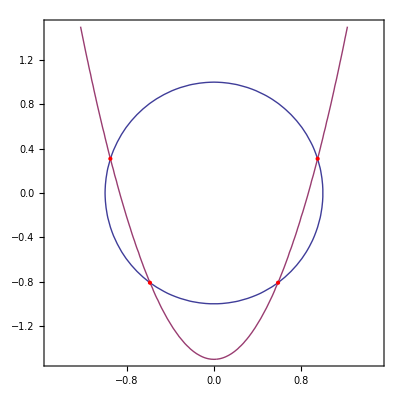

```mathematica
Show[{ContourPlot[{x^2+y^2==1,y-2x^2+3/2==0},{x,-1.5,1.5},{y,-1.5,1.5}],Graphics[{Red,PointSize[Medium],Point[{x,y}/.pts]}]}]
```

Find conditions for a quartic to have all roots equal:

```mathematica
f[x_]:= x^4 + a x^3 + b x^2 + c x + d
```

A method using Subresultantspaclet:ref/Subresultants:

```mathematica
Solve[Thread[Drop[Subresultants[f[x],D[f[x],x],x],-1]==0],{b,c,d}]
```

{{b→(3 a^2)/8,c→a^3/16,d→a^4/256}}

A method using quantifier elimination:

```mathematica
Solve[Exists[x,f[x]==0,ForAll[y,f[y]==0, x==y]],{b,c,d}]
```

{{b→(3 a^2)/8,c→a^3/16,d→a^4/256}}

Plot a space curve given by an implicit description:

```mathematica
curve=x^2+y^2+z^2==1&&x^3+x y^2==z^2;
```

```mathematica
sol=Solve[curve,{y,z},Reals]
```

{{y→ConditionalExpression[-√((1-x^2-x^3)/(1+x)),0<x<1/3 (-1+(25/2-(3 √69)/2)^(1/3)+(1/2 (25+3 √69))^(1/3))],z→ConditionalExpression[-√(x^3+(x (1-x^2-x^3))/(1+x)),0<x<1/3 (-1+(25/2-(3 √69)/2)^(1/3)+(1/2 (25+3 √69))^(1/3))]},{y→ConditionalExpression[-√((1-x^2-x^3)/(1+x)),0<x<1/3 (-1+(25/2-(3 √69)/2)^(1/3)+(1/2 (25+3 √69))^(1/3))],z→ConditionalExpression[√(x^3+(x (1-x^2-x^3))/(1+x)),0<x<1/3 (-1+(25/2-(3 √69)/2)^(1/3)+(1/2 (25+3 √69))^(1/3))]},{y→ConditionalExpression[√((1-x^2-x^3)/(1+x)),0<x<1/3 (-1+(25/2-(3 √69)/2)^(1/3)+(1/2 (25+3 √69))^(1/3))],z→ConditionalExpression[-√(x^3+(x (1-x^2-x^3))/(1+x)),0<x<1/3 (-1+(25/2-(3 √69)/2)^(1/3)+(1/2 (25+3 √69))^(1/3))]},{y→ConditionalExpression[√((1-x^2-x^3)/(1+x)),0<x<1/3 (-1+(25/2-(3 √69)/2)^(1/3)+(1/2 (25+3 √69))^(1/3))],z→ConditionalExpression[√(x^3+(x (1-x^2-x^3))/(1+x)),0<x<1/3 (-1+(25/2-(3 √69)/2)^(1/3)+(1/2 (25+3 √69))^(1/3))]}}

```mathematica
cond=Union[#[[2]]&/@Cases[sol, _ConditionalExpression, Infinity]]
```

{0<x<1/3 (-1+(25/2-(3 √69)/2)^(1/3)+(1/2 (25+3 √69))^(1/3))}

```mathematica
{l,u}=N[{cond[[1,1]],cond[[1,5]]}]
```

{0.,0.754878}

```mathematica
ParametricPlot3D[{x,y,z}/.sol,{x,l,u}]
```

-Graphics-

Plot the projection of the space curve on the {x,y} plane:

```mathematica
proj=Solve[Exists[z,curve],y,Reals]
```

{{y→ConditionalExpression[-√((1-x^2-x^3)/(1+x)),0<x<1/3 (-1+(25/2-(3 √69)/2)^(1/3)+(1/2 (25+3 √69))^(1/3))]},{y→ConditionalExpression[√((1-x^2-x^3)/(1+x)),0<x<1/3 (-1+(25/2-(3 √69)/2)^(1/3)+(1/2 (25+3 √69))^(1/3))]}}

```mathematica
ParametricPlot[{x,y}/.proj,{x,l,u}]
```

-Graphics-

Find a Pythagorean triple:

```mathematica
Solve[x^2+y^2==5^2&&y>x>0,{x,y},Integers]
```

{{x→3,y→4}}

Find a sequence of Pythagorean triples:

```mathematica
Table[Solve[x^2+y^2==z^2&&y>x>0,{x,y},Integers],{z,30}]
```

{{},{},{},{},{{x→3,y→4}},{},{},{},{},{{x→6,y→8}},{},{},{{x→5,y→12}},{},{{x→9,y→12}},{},{{x→8,y→15}},{},{},{{x→12,y→16}},{},{},{},{},{{x→7,y→24},{x→15,y→20}},{{x→10,y→24}},{},{},{{x→20,y→21}},{{x→18,y→24}}}

Find how to pay $2.27 postage with 10-, 23-, and 37-cent stamps:

```mathematica
Solve[a 10 + b 23 + c 37 == 227 &&a>=0&&b>=0&&c>=0,{a,b,c},Integers]
```

{{a→1,b→3,c→4},{a→2,b→9,c→0},{a→7,b→2,c→3},{a→13,b→1,c→2},{a→19,b→0,c→1}}

The same task can be accomplished with IntegerPartitionspaclet:ref/IntegerPartitions:

```mathematica
IntegerPartitions[227,All,{37,23,10}]
```

{{10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,37},{10,10,10,10,10,10,10,10,10,10,10,10,10,23,37,37},{10,10,10,10,10,10,10,23,23,37,37,37},{10,10,23,23,23,23,23,23,23,23,23},{10,23,23,23,37,37,37,37}}

### Properties & Relations (14)

Solutions satisfy the equations:

```mathematica
eqns={x^2+y^2==1&&2x+3y==4};
Solve[eqns,{x,y}]
```

{{x→1/13 (8-3 ⅈ √3),y→2/13 (6+ⅈ √3)},{x→1/13 (8+3 ⅈ √3),y→2/13 (6-ⅈ √3)}}

Solutions are given as replacement rules and can be directly used for substitution:

```mathematica
eqns/.%
```

{{True},{True}}

Solvepaclet:ref/Solve uses {} to represent the empty solution or no solution:

```mathematica
Solve[x==1&&x==2,x]
```

{}

Solvepaclet:ref/Solve uses {{}} to represent the universal solution or all points satisfying the equations:

```mathematica
Solve[x==x,x]
```

{{}}

For univariate equations, Solvepaclet:ref/Solve repeats solutions according to their multiplicity:

```mathematica
Solve[(x-1)^2(x-2)^3==0,x]
```

{{x→1},{x→1},{x→2},{x→2},{x→2}}

Solutions of algebraic equations are often given in terms of Rootpaclet:ref/Root objects:

```mathematica
Solve[x^5-2x+7==0,x]
```

{{x→Root[7-2 #1+#1^5&,1]},{x→Root[7-2 #1+#1^5&,2]},{x→Root[7-2 #1+#1^5&,3]},{x→Root[7-2 #1+#1^5&,4]},{x→Root[7-2 #1+#1^5&,5]}}

Use Npaclet:ref/N to compute numeric approximations of Rootpaclet:ref/Root objects:

```mathematica
N[%,20]
```

{{x→-1.5905953731967206259},{x→-0.3641060494347463171-1.4820021939508159206 ⅈ},{x→-0.3641060494347463171+1.4820021939508159206 ⅈ},{x→1.1594037360331066301-0.7385503070914527752 ⅈ},{x→1.1594037360331066301+0.7385503070914527752 ⅈ}}

Rootpaclet:ref/Root objects may involve parameters:

```mathematica
Solve[x^5+a x+1==0,x]
```

{{x→Root[1+a #1+#1^5&,1]},{x→Root[1+a #1+#1^5&,2]},{x→Root[1+a #1+#1^5&,3]},{x→Root[1+a #1+#1^5&,4]},{x→Root[1+a #1+#1^5&,5]}}

Use Seriespaclet:ref/Series to compute series expansions of Rootpaclet:ref/Root objects:

```mathematica
Series[x/.%[[1]],{a,0,10}]
```

-1+a/5+a^2/25+a^3/125-(21 a^5)/15625-(78 a^6)/78125-(187 a^7)/390625-(286 a^8)/1953125+(9367 a^10)/244140625+O[a]^11

The series satisfies the equation up to order 11:

```mathematica
x^5+a x+1/.x->%
```

O[a]^11

Find solutions over specified domains:

```mathematica
Solve[(x^4-1)(x^4-4)==0,x]
```

{{x→-1},{x→-ⅈ},{x→ⅈ},{x→1},{x→-√2},{x→-ⅈ √2},{x→ⅈ √2},{x→√2}}

```mathematica
Solve[(x^4-1)(x^4-4)==0,x,Reals]
```

{{x→-1},{x→1},{x→-√2},{x→√2}}

```mathematica
Solve[(x^4-1)(x^4-4)==0,x,Integers]
```

{{x→-1},{x→1}}

Solutions may involve conditions on parameters:

```mathematica
Solve[x^2+a x+b==0,x,Reals]
```

{{x→ConditionalExpression[-a/2-1/2 √(a^2-4 b),b<a^2/4]},{x→ConditionalExpression[-a/2+1/2 √(a^2-4 b),b<a^2/4]}}

Conditional solutions satisfy the equations, provided the conditions are satisfied:

```mathematica
Expand[x^2+a x+b==0/.%]
```

{ConditionalExpression[True,b<a^2/4],ConditionalExpression[True,b<a^2/4]}

Solvepaclet:ref/Solve represents solutions in terms of replacement rules:

```mathematica
Solve[x^4==4,x]
```

{{x→-√2},{x→-ⅈ √2},{x→ⅈ √2},{x→√2}}

Reducepaclet:ref/Reduce represents solutions in terms of Boolean combinations of equations and inequalities:

```mathematica
Reduce[x^4==4,x]
```

x==-√2||x==-ⅈ √2||x==ⅈ √2||x==√2

Solvepaclet:ref/Solve uses fast heuristics to solve transcendental equations, but may give incomplete solutions:

```mathematica
Solve[x-E^x==1, x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1-ProductLog[-ⅇ]}}

```mathematica
Solve[x Log[x]==a,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→a/ProductLog[a]}}

Reducepaclet:ref/Reduce uses methods that are often slower, but finds all solutions and gives all necessary conditions:

```mathematica
Reduce[x-E^x==1,x]
```

C[1]∈Integers&&x==1-ProductLog[C[1],-ⅇ]

```mathematica
Reduce[x Log[x]==a,x]
```

(a≠0&&((Im[ProductLog[-1,a]]>-π&&x==ⅇ^ProductLog[-1,a])||x==ⅇ^ProductLog[a]||(Im[ProductLog[1,a]]≤π&&x==ⅇ^ProductLog[1,a])))||(a==0&&x==1)

Use FindInstancepaclet:ref/FindInstance to find solution instances:

```mathematica
FindInstance[x^2+y^2+z^2==1&&2x y==z^3,{x,y,z}]
```

{{x→2,y→Root[27+43 #1^2+9 #1^4+#1^6&,1],z→Root[{27+43 #1^2+9 #1^4+#1^6&,25 #1+6 #1^3+#1^5+12 #2&},{1,1}]}}

Like Reducepaclet:ref/Reduce, FindInstancepaclet:ref/FindInstance can be given inequalities and domain specifications:

```mathematica
FindInstance[x^2-3y^2==1&&0<x<10^10,{x,y},Integers,3]
```

{{x→708158977,y→408855776},{x→2642885282,y→-1525870529},{x→978122,y→564719}}

Use DSolvepaclet:ref/DSolve to solve differential equations:

```mathematica
DSolve[y''[x]==-y[x],y[x],x]
```

{{y[x]→C[1] Cos[x]+C[2] Sin[x]}}

```mathematica
DSolve[{y''[x]==-y[x],y[0]==0,y'[0]==1},y[x],x]
```

{{y[x]→Sin[x]}}

Use RSolvepaclet:ref/RSolve to solve recurrence equations:

```mathematica
RSolve[f[n+1]==n f[n],f[n],n]
```

{{f[n]→C[1] Pochhammer[1,-1+n]}}

```mathematica
RSolve[{f[n+1]==n+f[n],f[0]==0},f[n],n]
```

{{f[n]→1/2 (-1+n) n}}

SolveAlwayspaclet:ref/SolveAlways gives the values of parameters for which complex equations are always true:

```mathematica
SolveAlways[(a -2b+1)x^2+(a-b^2-c)x ==a^2-b+3c-1,x]
```

{{a→-2-√13,b→1/2 (-1-√13),c→1/2 (-11-3 √13)},{a→-2+√13,b→1/2 (-1+√13),c→-11/2+(3 √13)/2}}

The same problem can be expressed using ForAllpaclet:ref/ForAll and solved with Solvepaclet:ref/Solve or Reducepaclet:ref/Reduce:

```mathematica
Solve[ForAll[x,(a -2b+1)x^2+(a-b^2-c)x ==a^2-b+3c-1],{a,b,c}]
```

{{a→-2-√13,b→1/2 (-1-√13),c→1/2 (-11-3 √13)},{a→-2+√13,b→1/2 (-1+√13),c→1/2 (-11+3 √13)}}

```mathematica
Reduce[ForAll[x,(a -2b+1)x^2+(a-b^2-c)x ==a^2-b+3c-1],{a,b,c}]
```

(a==-2-√13||a==-2+√13)&&b==(1+a)/2&&c==1/2 (-5+3 a)

Resolvepaclet:ref/Resolve eliminates quantifiers, possibly without solving the resulting quantifier-free system:

```mathematica
Resolve[Exists[x,x^2+y^2+z^2==1&&x y>z^3],Reals]
```

(z<0&&y^2+z^2≤1)||(y^2+z^2≤1&&-y^2+y^4+y^2 z^2+z^6<0)

```mathematica
Resolve[ForAll[{x,y},a x^2+b x+c==0&&a y^2+b y+c==0,x==y]]
```

(a==0&&b≠0)||(a==0&&c≠0)||(a≠0&&b^2-4 a c==0)

Eliminatepaclet:ref/Eliminate eliminates variables from systems of complex equations:

```mathematica
Eliminate[x^2+y^2+z^2==1&&x z==y^3,x]
```

(-1+y^2) z^2+z^4==-y^6

This solves the same problem using Resolvepaclet:ref/Resolve:

```mathematica
Resolve[Exists[x,x^2+y^2+z^2==1&&x z==y^3]]
```

(y==0&&z==0)||(z≠0&&y^6-z^2+y^2 z^2+z^4==0)

Reducepaclet:ref/Reduce and Solvepaclet:ref/Solve additionally solve the resulting equations:

```mathematica
Reduce[Exists[x,x^2+y^2+z^2==1&&x z==y^3],{y,z}]
```

(y==0&&z==0)||((z==-(√(1-y^2-√(1-2 y^2+y^4-4 y^6)))/(√2)||z==(√(1-y^2-√(1-2 y^2+y^4-4 y^6)))/(√2)||z==-(√(1-y^2+√(1-2 y^2+y^4-4 y^6)))/(√2)||z==(√(1-y^2+√(1-2 y^2+y^4-4 y^6)))/(√2))&&z≠0)

```mathematica
Solve[Exists[x,x^2+y^2+z^2==1&&x z==y^3],z]
```

{{z→-(√(1-y^2-√(1-2 y^2+y^4-4 y^6)))/(√2)},{z→(√(1-y^2-√(1-2 y^2+y^4-4 y^6)))/(√2)},{z→-(√(1-y^2+√(1-2 y^2+y^4-4 y^6)))/(√2)},{z→(√(1-y^2+√(1-2 y^2+y^4-4 y^6)))/(√2)}}

### Possible Issues (4)

Solvepaclet:ref/Solve gives generic solutions; solutions involving equations on parameters are not given:

```mathematica
Solve[a x^2+x==1,x]
```

{{x→(-1-√(1+4 a))/(2 a)},{x→(-1+√(1+4 a))/(2 a)}}

Reducepaclet:ref/Reduce gives all solutions, including those that require equations on parameters:

```mathematica
Reduce[a x^2+x==1,x]
```

(a==0&&x==1)||(a≠0&&(x==(-1-√(1+4 a))/(2 a)||x==(-1+√(1+4 a))/(2 a)))

With MaxExtraConditionspaclet:ref/MaxExtraConditions->Allpaclet:ref/All, Solvepaclet:ref/Solve also gives non-generic solutions:

```mathematica
Solve[a x^2+x==1,x,MaxExtraConditions->All]
```

{{x→ConditionalExpression[1,a==0]},{x→ConditionalExpression[(-1-√(1+4 a))/(2 a),a≠0]},{x→ConditionalExpression[(-1+√(1+4 a))/(2 a),a≠0]}}

Solvepaclet:ref/Solve results do not depend on whether some of the input equations contain only parameters. The following two systems are equivalent and have no generic solutions:

```mathematica
Solve[x==1&& a==2,x]
```

{}

```mathematica
Solve[x==1&&x+a==x+2,x]
```

{}

Use MaxExtraConditionspaclet:ref/MaxExtraConditions to specify the number of parameter conditions allowed:

```mathematica
Solve[x==1&& a==2,x,MaxExtraConditions->1]
```

{{x→ConditionalExpression[1,a==2]}}

```mathematica
Solve[x==1&& x+a==x+2,x,MaxExtraConditions->1]
```

{{x→ConditionalExpression[1,a==2]}}

Use the Existspaclet:ref/Exists quantifier to find solutions that are valid for some value of parameter a:

```mathematica
Solve[Exists[a,x==1&& a==2],x]
```

{{x→1}}

```mathematica
Solve[Exists[a,x==1&& x+a==x+2],x]
```

{{x→1}}

Solvepaclet:ref/Solve does not eliminate solutions that are neither generically correct nor generically incorrect:

```mathematica
Solve[Sqrt[((1-z)/(1+z))^2]==(1-a)/(1+a),z]
```

{{z→1/a},{z→a}}

The solutions are correct for 0<|a|<1 and incorrect for |a|>1:

```mathematica
Sqrt[((1-z)/(1+z))^2]-(1-a)/(1+a)/.%/.{{a->(2+3I)/4},{a->2+3I}}
```

{{0,0},{4/3+(2 ⅈ)/3,4/3+(2 ⅈ)/3}}

For transcendental equations Solvepaclet:ref/Solve may not give all solutions:

```mathematica
Solve[x+E^x==1/2,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1/2 (1-2 ProductLog[√ⅇ])}}

Use Reducepaclet:ref/Reduce to get all solutions:

```mathematica
Reduce[x+E^x==1/2,x]
```

C[1]∈Integers&&x==1/2-ProductLog[C[1],√ⅇ]

Solvepaclet:ref/Solve with Methodpaclet:ref/Method->"Reduce" uses Reducepaclet:ref/Reduce to find solutions, but returns replacement rules:

```mathematica
Solve[x+E^x==1/2,x,Method->"Reduce"]
```

{{x→ConditionalExpression[1/2-ProductLog[C[1],√ⅇ],C[1]∈Integers]}}

Using inverse functions allows Solvepaclet:ref/Solve to find some solutions fast:

```mathematica
Solve[x^n==1,x]//Timing
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{0.03125,{{x→1}}}

Finding the complete solution may take much longer and the solution may be large:

```mathematica
(red=Reduce[x^n==1,x])//LeafCount//Timing
```

{5.3125,611}

This finds the values of n for which x==2 is a solution:

```mathematica
Reduce[red/.x->2,n]
```

(C[1]∈Integers&&n==0)||(C[1]∈Integers&&C[1]≥1&&n==(2 ⅈ π C[1])/Log[2])||(C[1]∈Integers&&C[1]≤-1&&n==(2 ⅈ π C[1])/Log[2])

```mathematica
Simplify[x^n/.{x->2,n->2I Pi C[1]/Log[2]},Element[C[1],Integers]]
```

1

## See Also

Rootpaclet:ref/Root  ▪  Reducepaclet:ref/Reduce  ▪  FindInstancepaclet:ref/FindInstance  ▪  NSolvepaclet:ref/NSolve  ▪  FindRootpaclet:ref/FindRoot  ▪  Eliminatepaclet:ref/Eliminate  ▪  SolveAlwayspaclet:ref/SolveAlways  ▪  LinearSolvepaclet:ref/LinearSolve  ▪  RowReducepaclet:ref/RowReduce  ▪  ToRadicalspaclet:ref/ToRadicals  ▪  GroebnerBasispaclet:ref/GroebnerBasis  ▪  CylindricalDecompositionpaclet:ref/CylindricalDecomposition  ▪  DSolvepaclet:ref/DSolve  ▪  RSolvepaclet:ref/RSolve  ▪  ContourPlotpaclet:ref/ContourPlot  ▪  ContourPlot3Dpaclet:ref/ContourPlot3D  ▪  RegionPlotpaclet:ref/RegionPlot  ▪  RegionPlot3Dpaclet:ref/RegionPlot3D

## Tutorials

Symbolic Mathematics: Basic Operationspaclet:tutorial/SymbolicCalculations

Solving Equationspaclet:tutorial/SolvingEquations

Simultaneous Equationspaclet:tutorial/SimultaneousEquations

Solving Equations Involving Power Seriespaclet:tutorial/SolvingEquationsInvolvingPowerSeries

Solving Linear Systemspaclet:tutorial/SolvingLinearSystems

Solving Logical Combinations of Equationspaclet:tutorial/SolvingLogicalCombinationsOfEquations

Generic and Non-Generic Solutionspaclet:tutorial/GenericAndNonGenericSolutions

Eliminating Variablespaclet:tutorial/EliminatingVariables

## Related Guides

Additive Number Theorypaclet:guide/AdditiveNumberTheory

Equation Solvingpaclet:guide/EquationSolving

Polynomial Algebrapaclet:guide/PolynomialAlgebra

Polynomial Equationspaclet:guide/PolynomialEquations

Polynomial Systemspaclet:guide/PolynomialSystems

Precollege Educationpaclet:guide/PrecollegeEducation

Summary of New Features in Mathematica 8paclet:guide/SummaryOfNewFeaturesIn80

New in 8.0: Mathematics & Algorithmspaclet:guide/NewIn80MathematicsAndAlgorithms

## Related Links

Demonstrations with Solvehttp://demonstrations.wolfram.com/symbol.html?symbol=Solve (Wolfram Demonstrations Projecthttp://demonstrations.wolfram.com/)